Just a note: this notebook is quite similar to Jupyter notebooks (they are the inspiration), so bear that in mind as you edit and, more importantly, always remember shift+enter lol. All built in functions (there are a LOT) are capitalized and if you start typing one in, you can immediately access the documentation (also LOTS).

Set parameters:

```mathematica
T=1.;
γ=10.;
b = Sqrt[2*γ*T];
tc=50;
ki=0.5;
kf=1;
dk=kf-ki;
```

```mathematica
k[t_]:=ki+dk*1/2(1+Erf[(t-tc)]);
dlogk=D[Log[k[t]],t];
```

Test in the harmonic case/check syntax. The ItoProcess functions define the integration problem

```mathematica
harmonic=ItoProcess[{
ⅆx[t]== vx[t]ⅆt,
ⅆvx[t]== (-γ*vx[t]-k[t]*x[t])ⅆt+b*ⅆw1[t]},
x[t],{{x,vx},{0,0}},t,w1\[Distributed]WienerProcess[]];
```

```mathematica
harmonicese=ItoProcess[{
ⅆx[t]== vx[t]ⅆt,
ⅆvx[t]== (-γ/2*dlogk*x[t]-γ*vx[t]-k[t]*x[t])ⅆt+b*ⅆw1[t]},
x[t],{{x,vx},{0,0}},t,w1\[Distributed]WienerProcess[]];
```

Now we actually integrate the Ito integrals with a step size of 0.01 and 500 simulations

```mathematica
harmonicsim= RandomFunction[harmonic,{0.,100,0.01},500]
harmonicesesim= RandomFunction[harmonicese,{0.,100,0.01},500]
```

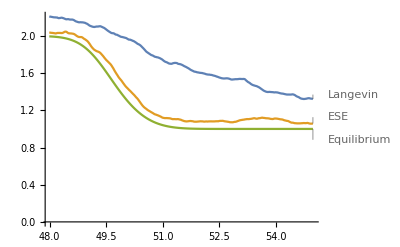

```mathematica
ListLinePlot[{Table[{(i-1)*0.01,Variance[Normal[harmonicsim][[All,i,2]]]},{i,4800,5500}],Table[{(i-1)*0.01,Variance[Normal[harmonicesesim][[All,i,2]]]},{i,4800,5500}],Table[{(i-1)*0.01,T/k[(i-1)*0.01]},{i,4800,5500}]},PlotLabels->{"Langevin","ESE","Equilibrium"}]
```

The beauty of doing this in Mathematica is the ease and speed (admittedly giving up some of the knowledge of what’s happening under the hood) and the extraordinarily sophisticated built-in plotting.

Okay onto the anharmonic:

```mathematica
anharmonic=ItoProcess[{
ⅆx[t]== vx[t]ⅆt,
ⅆy[t]== vy[t]ⅆt,
ⅆz[t]== vz[t]ⅆt,
ⅆvx[t]== (-γ*vx[t]-k[t]*(x[t]^2+y[t]^2+z[t]^2)x[t])ⅆt+b*ⅆw1[t],
ⅆvy[t]== (-γ*vy[t]-k[t]*(x[t]^2+y[t]^2+z[t]^2)y[t])ⅆt+b*ⅆw2[t],
ⅆvz[t]==(-γ*vz[t]-k[t]*(x[t]^2+y[t]^2+z[t]^2)z[t])ⅆt+b*ⅆw3[t]},
x[t],{{x,y,z,vx,vy,vz},{0,0,0,0,0,0}},t,{w1\[Distributed]WienerProcess[],w2\[Distributed]WienerProcess[],w3\[Distributed]WienerProcess[]}];
anharmonicese=ItoProcess[{
ⅆx[t]== vx[t]ⅆt,
ⅆy[t]== vy[t]ⅆt,
ⅆz[t]== vz[t]ⅆt,
ⅆvx[t]== (-γ/4*dlogk*x[t]-γ*vx[t]-k[t]*(x[t]^2+y[t]^2+z[t]^2)x[t])ⅆt+b*ⅆw1[t],
ⅆvy[t]== (-γ/4*dlogk*y[t]-γ*vy[t]-k[t]*(x[t]^2+y[t]^2+z[t]^2)y[t])ⅆt+b*ⅆw2[t],
ⅆvz[t]==(-γ/4*dlogk*z[t]-γ*vz[t]-k[t]*(x[t]^2+y[t]^2+z[t]^2)z[t])ⅆt+b*ⅆw3[t]},
x[t],{{x,y,z,vx,vy,vz},{0,0,0,0,0,0}},t,{w1\[Distributed]WienerProcess[],w2\[Distributed]WienerProcess[],w3\[Distributed]WienerProcess[]}];
```

```mathematica
anharmonicsim=RandomFunction[anharmonic,{0.,100.,0.01},1000]
anharmonicesesim=RandomFunction[anharmonicese,{0.,100.,0.01},1000]
```

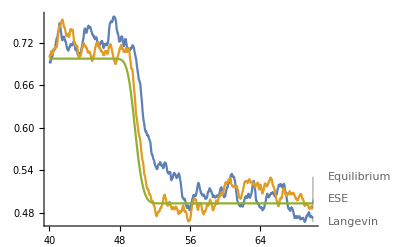

```mathematica
ListLinePlot[{Table[{(i-1)*0.01,Variance[Normal[anharmonicsim][[All,i,2]]]},{i,4000,7000}],Table[{(i-1)*0.01,Variance[Normal[anharmonicesesim][[All,i,2]]]},{i,4000,7000}],
Table[{(i-1)*0.01,Gamma[-3/4]/(2 Gamma[-1/4] √k[(i-1)*0.01])},{i,4000,7000}]},PlotLabels->{"Langevin","ESE","Equilibrium"}]
```

After many tries, I did the rotor in python because we need some under the hood stuff honestly. ESE will be tougher as a result unfortuntely but hopefully done tomorrow. Double pendula almost done (amenable to mathematica)